# Project report

## SFC: Valves reconfiguration

D Malan

Department of Chemistry
University of Pretoria

6 December 2019

## Introduction

The aim of this project is reconfigure the valves of the SFC for resumption of chromatographic runs. The valves were un-configured for the column flow experiment. This was necessary because there is no CO2 supply shut-off valve, so the system is always at CO2 pressure. Because I wanted to disconnect and re-connect columns I needed to be able to shut down the CO2 flow without depressurising the pump and losing all that expensive carbon dioxide.

## Experimental

The SFC pump was filled and set to a pressure of 200 atm. The flow trough the restrictor was measured.
“The choice was a simple linear restrictor and we trusted that heating the end of the restrictor would prevent discrimination. The final linear restrictor was 800mm long and had an internal diameter of 0.050mm.”1 “The SFC column we used in the SFC×GC system was ... HPLC columns (150mm × 4.6mm, 3μm particles) (Restek, Pinnacle DB Silica) connected in series.”2
The time taken for 50 ml of gaseous carbon dioxide to flow through a bubble flow meter was measured with a hand-held stopwatch, and typed into an Excel spreadsheet. 
The flow was measures under a few configurations.

With the modifier valve reconfigured, in the LOAD position.

With the modifier valve in the RUN position.

With the modifier valve in the RUN position and the sample valve in the INJECT position.

## Observations

The flow is not as stable as one would wish. For the first two sets the flow was reliable and repeatable, but for the last set the flow started being a little bit puffy. Clipping the tip of the restrictor did not make a noticeable difference.

## Data analysis

Import the data:

```mathematica
data=Import["\\\\chemserv\\CHEMBACK\\HPLC-GC\\Varian-SFC-x-GC#R2-26\\ANAL\\EgmontR\\Niel\\Dropbox\\2019_12_05_SFC_Flow.xlsx", "DataLegacy"];
```

```mathematica
data[[1]][[1;;]][[All,3;;]]//TableForm
```

|  |  | 
 |  |  | 
Column A L1 Column B L2 Column C L3 Column D L4 Column E |  |  | 
Fed via modifier valve and mixing chamber and sample valve. Modifier valve in "Load" position. |  |  | 
Volume of gas | Time | Time | Flow
ml | s | min | ml/min
50. | 6.98 | 0.116333 | 429.799
50. | 6.63 | 0.1105 | 452.489
50. | 6.84 | 0.114 | 438.596
50. | 6.88 | 0.114667 | 436.047
50. | 6.77 | 0.112833 | 443.131
50. | 6.88 | 0.114667 | 436.047
 |  |  | 
 |  |  | 
Column A L1 Column B L2 Column C L3 Column D L4 Column E |  |  | 
Fed via modifier valve and mixing chamber and sample valve. Modifier valve in "Run" position. |  |  | 
Volume of gas | Time | Time | Flow
ml | s | min | ml/min
50. | 6.92 | 0.115333 | 433.526
50. | 6.52 | 0.108667 | 460.123
50. | 6.85 | 0.114167 | 437.956
50. | 6.91 | 0.115167 | 434.153
50. | 7.06 | 0.117667 | 424.929
50. | 7.34 | 0.122333 | 408.719
 |  |  | 
 |  |  | 
Column A L1 Column B L2 Column C L3 Column D L4 Column E |  |  | 
Fed via modifier valve and mixing chamber and sample valve. Modifier valve in "Run" position. Sample valve in "Inject" position |  |  | 
Volume of gas | Time | Time | Flow
ml | s | min | ml/min
50. | 5.94 | 0.099 | 505.051
50. | 7.38 | 0.123 | 406.504
50. | 7.36 | 0.122667 | 407.609
50. | 7.42 | 0.123667 | 404.313
50. | 7.46 | 0.124333 | 402.145
50. | 7.31 | 0.121833 | 410.397
50. | 7.38 | 0.123 | 406.504
50. | 7.28 | 0.121333 | 412.088

Copy & paste data from the cell above

```mathematica
data1 =( {{429.79942693409737}, {452.4886877828054}, {438.59649122807014}, {436.04651162790697}, {443.1314623338257}, {436.04651162790697}})//Flatten
```

{429.799,452.489,438.596,436.047,443.131,436.047}

```mathematica
data2 = Flatten[({{433.52601156069363}, {460.1226993865031}, {437.95620437956205}, {434.1534008683068}, {424.929178470255}, {408.7193460490463}})]
```

{433.526,460.123,437.956,434.153,424.929,408.719}

```mathematica
data3= Flatten[({{505.050505050505}, {406.5040650406504}, {407.6086956521739}, {404.3126684636119}, {402.1447721179625}, {410.39671682626545}, {406.5040650406504}, {412.08791208791206}})]
```

{505.051,406.504,407.609,404.313,402.145,410.397,406.504,412.088}

```mathematica
flow1 = Join[Split[data1],Table[1, Length[data1],1],2]
```

{{429.799,1},{452.489,1},{438.596,1},{436.047,1},{443.131,1},{436.047,1}}

```mathematica
flow2 = Join[Split[data2],Table[2, Length[data2],1],2]
```

{{433.526,2},{460.123,2},{437.956,2},{434.153,2},{424.929,2},{408.719,2}}

```mathematica
flow3 = Join[Split[data3],Table[3, Length[data3],1],2]
```

{{505.051,3},{406.504,3},{407.609,3},{404.313,3},{402.145,3},{410.397,3},{406.504,3},{412.088,3}}

```mathematica
flow = Join[flow1, flow2, flow3]
```

{{429.799,1},{452.489,1},{438.596,1},{436.047,1},{443.131,1},{436.047,1},{433.526,2},{460.123,2},{437.956,2},{434.153,2},{424.929,2},{408.719,2},{505.051,3},{406.504,3},{407.609,3},{404.313,3},{402.145,3},{410.397,3},{406.504,3},{412.088,3}}

```mathematica
flowavg =MapIndexed[ {Mean[#1],#2[[1]]}&, {data1, data2, data3}]
```

{{439.352,1},{433.234,2},{419.326,3}}

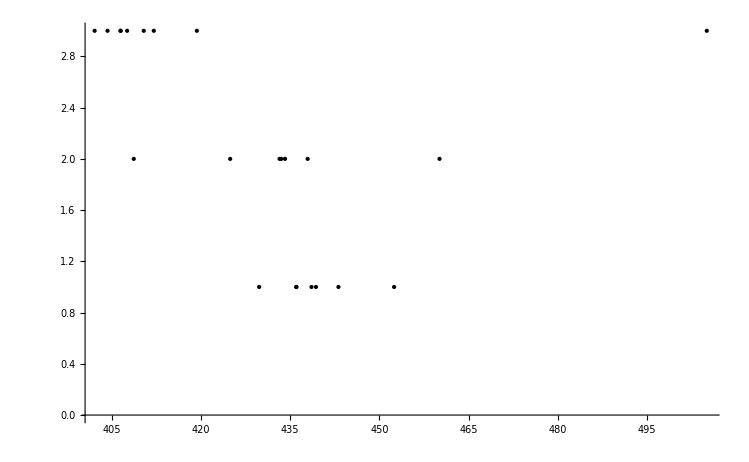

```mathematica
ListPlot[{flow, flowavg},PlotStyle->{Blue, {Red, PointSize[0.02], ChartLabels->{0,0,1,2}}}]
```

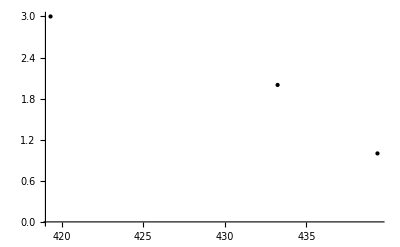

```mathematica
flowavgplot = ListPlot[flowavg, PlotStyle->{Red, PointSize[0.02]}]
```

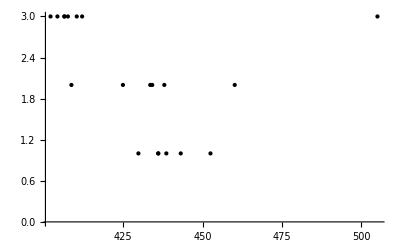

```mathematica
flowplot = ListPlot[flow]
```

Combine the graphics:

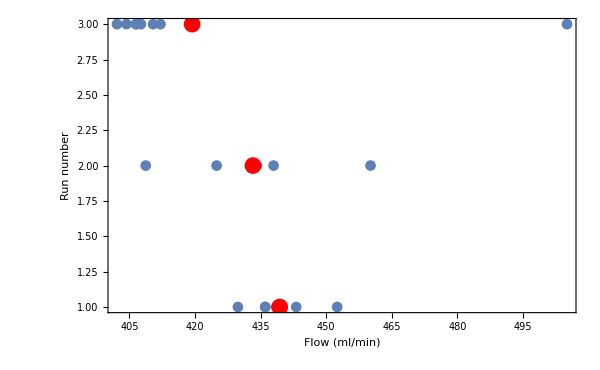

```mathematica
Show[flowplot
, flowavgplot

,PlotStyle->{Automatic, {Red, PointSize[0.09]}}
,Axes->False
,Frame->{True, True, False, False}
,FrameLabel->{Style["Flow (ml/min)", Large, Black,Bold], Style["Run number", Large, Black, Bold]}
,FrameStyle->Directive[Medium, Bold, Black]
, ImageSize-> 600
,PlotRange ->{ Automatic,Automatic}]
```

## Results

The figure above summarizes the results. There is some variation in the flow for the different runs.

## Bibliography

1	Malan, Daniel. 2019. "Fast temperature programmed chromatography coupled to supercritical fluid chromatography (SFC×GC)."

2	Malan, Daniel. 2019. "Fast temperature programmed chromatography coupled to supercritica fluid chromatography (SFC×GC)."

3	https://mathematica.stackexchange.com/questions/8997/cut-and-paste-data-from-a-spreadsheet